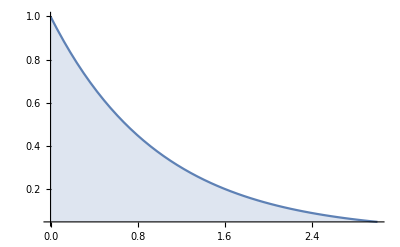

```mathematica
{{Plot[Table[PDF[ExponentialDistribution[λ],x],{λ,{1}}]//Evaluate,{x,0,3},Filling->Axis,PlotRange->All]}, {□}}
```

```mathematica
g = RandomVariate[ExponentialDistribution[1],100]
```

{1.48573,0.0264013,0.139511,1.85555,2.17346,1.28147,0.75696,1.37443,0.275218,0.564223,2.26077,0.0257737,1.16446,0.948721,0.193775,0.0545282,0.404741,0.587361,1.86994,1.12385,0.236377,2.72952,1.5977,1.42296,0.781716,0.477533,1.89454,0.421325,0.8885,0.640883,0.390345,0.794582,0.476922,1.58568,1.26048,0.175319,0.147979,0.756278,0.101933,0.373372,4.23615,0.123367,0.934628,0.222722,0.0889301,0.445854,0.523057,0.361036,0.37118,1.46985,1.22064,0.139602,1.29194,1.52488,1.63625,0.2008,1.55271,1.44695,0.727359,3.09525,4.81988,3.226,0.21401,0.805419,0.0771739,0.222813,0.295701,0.285736,1.09148,0.613861,0.21206,1.08581,0.327122,0.480481,0.406605,2.1641,0.514905,0.880799,0.22157,0.60986,0.129946,1.30974,1.15434,0.453328,0.303714,1.87877,0.206021,3.7788,1.32232,0.818544,0.431739,0.83099,2.43253,0.881508,0.603319,0.485526,0.21186,0.498747,0.705277,0.0660557}

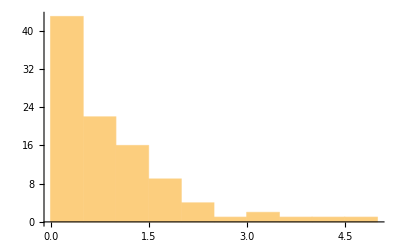

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

```mathematica
Histogram[g]
```

```mathematica
ld=LearnDistribution[{1.4857262042622308,0.026401251616819044,0.13951134938158838,1.8555477556329627,2.173459236516041,1.28146659745299,0.7569602143687342,1.3744321835984097,0.2752175944067963,0.5642230307194656,2.2607688725669446,0.02577371412605919,1.1644646446901166,0.9487206506228961,0.1937748804015464,0.05452818154542314,0.4047408248451862,0.5873608523831312,1.869939215856786,1.1238515760843408,0.23637678612544066,2.729523275346087,1.5976995956817255,1.422960658313398,0.7817155719927376,0.47753347937551865,1.8945371523760144,0.4213249290627868,0.8885001046890695,0.6408826059124343,0.3903451701057148,0.7945819914444694,0.4769222524078531,1.585677093475632,1.260484857730589,0.17531903309316696,0.14797907385661388,0.7562775427880811,0.10193266093316086,0.3733720992267179,4.236147288008292,0.12336692412236482,0.9346282818279117,0.22272186371374567,0.08893009364250853,0.4458542364437851,0.5230572406198697,0.36103641366994393,0.3711797358875362,1.4698534793618028,1.2206417962472207,0.1396023523701508,1.2919401510278798,1.5248802928911174,1.6362534124003818,0.20079982656205697,1.5527085611955957,1.4469453478523961,0.7273586581280115,3.095251311401037,4.819880999401546,3.225997422661187,0.2140102694891352,0.8054191590770747,0.07717385982024756,0.2228127578248376,0.29570118133590256,0.28573641672130373,1.0914813586603744,0.6138611161774729,0.21205991137090532,1.085805677692539,0.32712242518605844,0.4804809951721966,0.4066054243669081,2.164097231710444,0.5149051917238099,0.8807985745188566,0.22157032996407366,0.609859981830065,0.1299464125809985,1.3097375652787764,1.1543380195273585,0.4533276881750505,0.30371405807420265,1.8787716120022901,0.20602116630314266,3.7787962272260964,1.322321396272543,0.8185443239369542,0.43173913233403527,0.8309899693720667,2.4325263429621495,0.8815079282655907,0.6033186863981942,0.485525769413497,0.21185992013794763,0.49874676289742986,0.7052771183254212,0.06605572281751235},Method->"GaussianMixture"]
```

```mathematica
Plot[PDF[ld],1]
```

System`ProtoPlotDump`iPlot[Plot,System`ProtoPlotDump`obj$17817,PDF[ld],1]

```mathematica
LD =LearnDistribution[{1.4857262042622308,0.026401251616819044,0.13951134938158838,1.8555477556329627,2.173459236516041,1.28146659745299,0.7569602143687342,1.3744321835984097,0.2752175944067963,0.5642230307194656,2.2607688725669446,0.02577371412605919,1.1644646446901166,0.9487206506228961,0.1937748804015464,0.05452818154542314,0.4047408248451862,0.5873608523831312,1.869939215856786,1.1238515760843408,0.23637678612544066,2.729523275346087,1.5976995956817255,1.422960658313398,0.7817155719927376,0.47753347937551865,1.8945371523760144,0.4213249290627868,0.8885001046890695,0.6408826059124343,0.3903451701057148,0.7945819914444694,0.4769222524078531,1.585677093475632,1.260484857730589,0.17531903309316696,0.14797907385661388,0.7562775427880811,0.10193266093316086,0.3733720992267179,4.236147288008292,0.12336692412236482,0.9346282818279117,0.22272186371374567,0.08893009364250853,0.4458542364437851,0.5230572406198697,0.36103641366994393,0.3711797358875362,1.4698534793618028,1.2206417962472207,0.1396023523701508,1.2919401510278798,1.5248802928911174,1.6362534124003818,0.20079982656205697,1.5527085611955957,1.4469453478523961,0.7273586581280115,3.095251311401037,4.819880999401546,3.225997422661187,0.2140102694891352,0.8054191590770747,0.07717385982024756,0.2228127578248376,0.29570118133590256,0.28573641672130373,1.0914813586603744,0.6138611161774729,0.21205991137090532,1.085805677692539,0.32712242518605844,0.4804809951721966,0.4066054243669081,2.164097231710444,0.5149051917238099,0.8807985745188566,0.22157032996407366,0.609859981830065,0.1299464125809985,1.3097375652787764,1.1543380195273585,0.4533276881750505,0.30371405807420265,1.8787716120022901,0.20602116630314266,3.7787962272260964,1.322321396272543,0.8185443239369542,0.43173913233403527,0.8309899693720667,2.4325263429621495,0.8815079282655907,0.6033186863981942,0.485525769413497,0.21185992013794763,0.49874676289742986,0.7052771183254212,0.06605572281751235},Method->"GaussianMixture"]
Plot[ld,{x,0,5}]
```

```mathematica
LearnDistribution[{1.4857262042622308,0.026401251616819044,0.13951134938158838,1.8555477556329627,2.173459236516041,1.28146659745299,0.7569602143687342,1.3744321835984097,0.2752175944067963,0.5642230307194656,2.2607688725669446,0.02577371412605919,1.1644646446901166,0.9487206506228961,0.1937748804015464,0.05452818154542314,0.4047408248451862,0.5873608523831312,1.869939215856786,1.1238515760843408,0.23637678612544066,2.729523275346087,1.5976995956817255,1.422960658313398,0.7817155719927376,0.47753347937551865,1.8945371523760144,0.4213249290627868,0.8885001046890695,0.6408826059124343,0.3903451701057148,0.7945819914444694,0.4769222524078531,1.585677093475632,1.260484857730589,0.17531903309316696,0.14797907385661388,0.7562775427880811,0.10193266093316086,0.3733720992267179,4.236147288008292,0.12336692412236482,0.9346282818279117,0.22272186371374567,0.08893009364250853,0.4458542364437851,0.5230572406198697,0.36103641366994393,0.3711797358875362,1.4698534793618028,1.2206417962472207,0.1396023523701508,1.2919401510278798,1.5248802928911174,1.6362534124003818,0.20079982656205697,1.5527085611955957,1.4469453478523961,0.7273586581280115,3.095251311401037,4.819880999401546,3.225997422661187,0.2140102694891352,0.8054191590770747,0.07717385982024756,0.2228127578248376,0.29570118133590256,0.28573641672130373,1.0914813586603744,0.6138611161774729,0.21205991137090532,1.085805677692539,0.32712242518605844,0.4804809951721966,0.4066054243669081,2.164097231710444,0.5149051917238099,0.8807985745188566,0.22157032996407366,0.609859981830065,0.1299464125809985,1.3097375652787764,1.1543380195273585,0.4533276881750505,0.30371405807420265,1.8787716120022901,0.20602116630314266,3.7787962272260964,1.322321396272543,0.8185443239369542,0.43173913233403527,0.8309899693720667,2.4325263429621495,0.8815079282655907,0.6033186863981942,0.485525769413497,0.21185992013794763,0.49874676289742986,0.7052771183254212,0.06605572281751235}]
```

LearnDistribution[{1.48573,0.0264013,0.139511,1.85555,2.17346,1.28147,0.75696,1.37443,0.275218,0.564223,2.26077,0.0257737,1.16446,0.948721,0.193775,0.0545282,0.404741,0.587361,1.86994,1.12385,0.236377,2.72952,1.5977,1.42296,0.781716,0.477533,1.89454,0.421325,0.8885,0.640883,0.390345,0.794582,0.476922,1.58568,1.26048,0.175319,0.147979,0.756278,0.101933,0.373372,4.23615,0.123367,0.934628,0.222722,0.0889301,0.445854,0.523057,0.361036,0.37118,1.46985,1.22064,0.139602,1.29194,1.52488,1.63625,0.2008,1.55271,1.44695,0.727359,3.09525,4.81988,3.226,0.21401,0.805419,0.0771739,0.222813,0.295701,0.285736,1.09148,0.613861,0.21206,1.08581,0.327122,0.480481,0.406605,2.1641,0.514905,0.880799,0.22157,0.60986,0.129946,1.30974,1.15434,0.453328,0.303714,1.87877,0.206021,3.7788,1.32232,0.818544,0.431739,0.83099,2.43253,0.881508,0.603319,0.485526,0.21186,0.498747,0.705277,0.0660557}]

```mathematica
LearnDistribution[{1.4857262042622308,0.026401251616819044,0.13951134938158838,1.8555477556329627,2.173459236516041,1.28146659745299,0.7569602143687342,1.3744321835984097,0.2752175944067963,0.5642230307194656,2.2607688725669446,0.02577371412605919,1.1644646446901166,0.9487206506228961,0.1937748804015464,0.05452818154542314,0.4047408248451862,0.5873608523831312,1.869939215856786,1.1238515760843408,0.23637678612544066,2.729523275346087,1.5976995956817255,1.422960658313398,0.7817155719927376,0.47753347937551865,1.8945371523760144,0.4213249290627868,0.8885001046890695,0.6408826059124343,0.3903451701057148,0.7945819914444694,0.4769222524078531,1.585677093475632,1.260484857730589,0.17531903309316696,0.14797907385661388,0.7562775427880811,0.10193266093316086,0.3733720992267179,4.236147288008292,0.12336692412236482,0.9346282818279117,0.22272186371374567,0.08893009364250853,0.4458542364437851,0.5230572406198697,0.36103641366994393,0.3711797358875362,1.4698534793618028,1.2206417962472207,0.1396023523701508,1.2919401510278798,1.5248802928911174,1.6362534124003818,0.20079982656205697,1.5527085611955957,1.4469453478523961,0.7273586581280115,3.095251311401037,4.819880999401546,3.225997422661187,0.2140102694891352,0.8054191590770747,0.07717385982024756,0.2228127578248376,0.29570118133590256,0.28573641672130373,1.0914813586603744,0.6138611161774729,0.21205991137090532,1.085805677692539,0.32712242518605844,0.4804809951721966,0.4066054243669081,2.164097231710444,0.5149051917238099,0.8807985745188566,0.22157032996407366,0.609859981830065,0.1299464125809985,1.3097375652787764,1.1543380195273585,0.4533276881750505,0.30371405807420265,1.8787716120022901,0.20602116630314266,3.7787962272260964,1.322321396272543,0.8185443239369542,0.43173913233403527,0.8309899693720667,2.4325263429621495,0.8815079282655907,0.6033186863981942,0.485525769413497,0.21185992013794763,0.49874676289742986,0.7052771183254212,0.06605572281751235}]
```

LearnDistribution[{1.48573,0.0264013,0.139511,1.85555,2.17346,1.28147,0.75696,1.37443,0.275218,0.564223,2.26077,0.0257737,1.16446,0.948721,0.193775,0.0545282,0.404741,0.587361,1.86994,1.12385,0.236377,2.72952,1.5977,1.42296,0.781716,0.477533,1.89454,0.421325,0.8885,0.640883,0.390345,0.794582,0.476922,1.58568,1.26048,0.175319,0.147979,0.756278,0.101933,0.373372,4.23615,0.123367,0.934628,0.222722,0.0889301,0.445854,0.523057,0.361036,0.37118,1.46985,1.22064,0.139602,1.29194,1.52488,1.63625,0.2008,1.55271,1.44695,0.727359,3.09525,4.81988,3.226,0.21401,0.805419,0.0771739,0.222813,0.295701,0.285736,1.09148,0.613861,0.21206,1.08581,0.327122,0.480481,0.406605,2.1641,0.514905,0.880799,0.22157,0.60986,0.129946,1.30974,1.15434,0.453328,0.303714,1.87877,0.206021,3.7788,1.32232,0.818544,0.431739,0.83099,2.43253,0.881508,0.603319,0.485526,0.21186,0.498747,0.705277,0.0660557}]

```mathematica
Information[LD]
```

Global`LD

LD=LearnDistribution[{1.48573,0.0264013,0.139511,1.85555,2.17346,1.28147,0.75696,1.37443,0.275218,0.564223,2.26077,0.0257737,1.16446,0.948721,0.193775,0.0545282,0.404741,0.587361,1.86994,1.12385,0.236377,2.72952,1.5977,1.42296,0.781716,0.477533,1.89454,0.421325,0.8885,0.640883,0.390345,0.794582,0.476922,1.58568,1.26048,0.175319,0.147979,0.756278,0.101933,0.373372,4.23615,0.123367,0.934628,0.222722,0.0889301,0.445854,0.523057,0.361036,0.37118,1.46985,1.22064,0.139602,1.29194,1.52488,1.63625,0.2008,1.55271,1.44695,0.727359,3.09525,4.81988,3.226,0.21401,0.805419,0.0771739,0.222813,0.295701,0.285736,1.09148,0.613861,0.21206,1.08581,0.327122,0.480481,0.406605,2.1641,0.514905,0.880799,0.22157,0.60986,0.129946,1.30974,1.15434,0.453328,0.303714,1.87877,0.206021,3.7788,1.32232,0.818544,0.431739,0.83099,2.43253,0.881508,0.603319,0.485526,0.21186,0.498747,0.705277,0.0660557},Method→GaussianMixture]

```mathematica
Plot[LD]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[LD]

```mathematica
Plot[LearnDistribution[{1.4857262042622308,0.026401251616819044,0.13951134938158838,1.8555477556329627,2.173459236516041,1.28146659745299,0.7569602143687342,1.3744321835984097,0.2752175944067963,0.5642230307194656,2.2607688725669446,0.02577371412605919,1.1644646446901166,0.9487206506228961,0.1937748804015464,0.05452818154542314,0.4047408248451862,0.5873608523831312,1.869939215856786,1.1238515760843408,0.23637678612544066,2.729523275346087,1.5976995956817255,1.422960658313398,0.7817155719927376,0.47753347937551865,1.8945371523760144,0.4213249290627868,0.8885001046890695,0.6408826059124343,0.3903451701057148,0.7945819914444694,0.4769222524078531,1.585677093475632,1.260484857730589,0.17531903309316696,0.14797907385661388,0.7562775427880811,0.10193266093316086,0.3733720992267179,4.236147288008292,0.12336692412236482,0.9346282818279117,0.22272186371374567,0.08893009364250853,0.4458542364437851,0.5230572406198697,0.36103641366994393,0.3711797358875362,1.4698534793618028,1.2206417962472207,0.1396023523701508,1.2919401510278798,1.5248802928911174,1.6362534124003818,0.20079982656205697,1.5527085611955957,1.4469453478523961,0.7273586581280115,3.095251311401037,4.819880999401546,3.225997422661187,0.2140102694891352,0.8054191590770747,0.07717385982024756,0.2228127578248376,0.29570118133590256,0.28573641672130373,1.0914813586603744,0.6138611161774729,0.21205991137090532,1.085805677692539,0.32712242518605844,0.4804809951721966,0.4066054243669081,2.164097231710444,0.5149051917238099,0.8807985745188566,0.22157032996407366,0.609859981830065,0.1299464125809985,1.3097375652787764,1.1543380195273585,0.4533276881750505,0.30371405807420265,1.8787716120022901,0.20602116630314266,3.7787962272260964,1.322321396272543,0.8185443239369542,0.43173913233403527,0.8309899693720667,2.4325263429621495,0.8815079282655907,0.6033186863981942,0.485525769413497,0.21185992013794763,0.49874676289742986,0.7052771183254212,0.06605572281751235},Method->"GaussianMixture"],1]
```